# ROBOT STANFORD PROGRAMA 2. CINEMÁTICA DIRECTA POR DENAVIT-HARTENBERG Y SIMULACIÓN POR CINEMÁTICA INVERSA MÉTODO NUMÉRICO.

Se obtienen las ecuaciones de cinemática directa a partir de la tabla de Denavit-Hartenberg, así como se validan utilizando el método numérico de Newton Raphson.

## FUNCIONES

```mathematica
(*FUNCIONES DE Matrices de Rotación 3x3 PARA CUALQUIER VARIABLE *)
Rx[α_]:={{1,0,0},{0,Cos[α], -Sin[α]}, {0,Sin[α], Cos[α]}};   
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0}, {-Sin[ϕ],0,Cos[ϕ]}};  
Rz[θ_]:={{Cos[θ], -Sin[θ],0},{Sin[θ], Cos[θ],0},{0,0,1}};
(*FUNCIONES de Matrices HOMEGENEAS de Traslación y Rotación 4x4 PARA CUALQUIER VARIABLE *)
Tx[x_]:={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
Ty[y_]:={{1,0,0,0},{0,1,0,y},{0,0,1,0},{0,0,0,1}}
Tz[z_]:={{1,0,0,0},{0,1,0,0},{0,0,1,z},{0,0,0,1}}
Qx[α_]:={{1,0,0,0},{0,Cos[α], -Sin[α], 0},{0, Sin[α], Cos[α],0},{0,0,0,1}}
Qy[ϕ_]:={{Cos[ϕ], 0, Sin[ϕ],0},{0,1,0,0},{-Sin[ϕ],0,Cos[ϕ],0},{0,0,0,1}}
Qz[θ_]:={{Cos[θ], -Sin[θ],0,0},{Sin[θ], Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}
(*FUNCIONES de Matrices HOMEGENEAS De Denavit-Hartenberg *)
Q[θ_, d_, a_, α_]:=Qz[θ].Tz[d].Tx[a].Qx[α]
Ma=Q[θ1, d1, a1, α1];
Ma//MatrixForm
(*FUNCIONES ADICIONALES *)
n={0,0,0,1};
T3D[P_]:={P⟦1⟧,P⟦2⟧,P⟦3⟧ }
M3D[Q_]:={{Q⟦1,1⟧,Q⟦1,2⟧, Q⟦1,3⟧ },{Q⟦2,1⟧,Q⟦2,2⟧, Q⟦2,3⟧},{Q⟦3,1⟧,Q⟦3,2⟧, Q⟦3,3⟧}}
T={{NX, OX, AX},{NY, OY, AY},{NZ, OZ, AZ}};
T//MatrixForm
(*Función para la evolución de las variables articulares*)
Grafica[tabla_, rojo_,verde_,azul_,EjeX_,EjeY_]:=ListPlot[tabla,ImageSize->300, Joined->True, PlotStyle->{AbsoluteThickness[6], RGBColor[rojo,verde,azul]},BaseStyle->{14,FontFamily->"Arial"}, Frame->True, FrameLabel->{EjeX,EjeY},GridLines->Automatic, PlotRange->All];
```

(Cos[θ1] | -Cos[α1] Sin[θ1] | Sin[α1] Sin[θ1] | a1 Cos[θ1]
Sin[θ1] | Cos[α1] Cos[θ1] | -Cos[θ1] Sin[α1] | a1 Sin[θ1]
0 | Sin[α1] | Cos[α1] | d1
0 | 0 | 0 | 1)

(NX | OX | AX
NY | OY | AY
NZ | OZ | AZ)

## CINEMÁTICA DIRECTA 5 GDL DENAVIT-HARTENBERG

## DH 14- OBTENER LAS MATRICES ^(i-1)A_i

```mathematica
Underoverscript[a, 1, 0]=Q[θ1, ℓ1, 0, 90°];
Underoverscript[a, 2, 1]=Q[90°+θ2, -ℓ2, 0, 90°];
Underoverscript[a, 3, 2]=Q[90°, d3, 0, 90°];
Underoverscript[a, 4, 3]=Q[θ4, 0, 0, -90°];
Underoverscript[a, 5, 4]=Q[θ5, ℓ5, 0, 0°];
```

## DH 15- OBTENER LAS MATRICES ^0 A_5=^0 A_1.^1 A_2.^2 A_3.....

```mathematica
Underoverscript[a, 2, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1]//Simplify;
Underoverscript[a, 3, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2]//Simplify;
Underoverscript[a, 4, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3]//Simplify;
Underoverscript[a, 5, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3].Underoverscript[a, 5, 4]//Simplify;
Underoverscript[a, 5, 0]//MatrixForm
```

(Cos[θ4] Cos[θ5] Sin[θ1]+Cos[θ1] (Cos[θ2] Cos[θ5] Sin[θ4]+Sin[θ2] Sin[θ5]) | Cos[θ1] Cos[θ5] Sin[θ2]-(Cos[θ4] Sin[θ1]+Cos[θ1] Cos[θ2] Sin[θ4]) Sin[θ5] | Cos[θ1] Cos[θ2] Cos[θ4]-Sin[θ1] Sin[θ4] | Cos[θ1] Cos[θ2] (d3+ℓ5 Cos[θ4])-Sin[θ1] (ℓ2+ℓ5 Sin[θ4])
-Cos[θ1] Cos[θ4] Cos[θ5]+Sin[θ1] (Cos[θ2] Cos[θ5] Sin[θ4]+Sin[θ2] Sin[θ5]) | Cos[θ5] Sin[θ1] Sin[θ2]+(Cos[θ1] Cos[θ4]-Cos[θ2] Sin[θ1] Sin[θ4]) Sin[θ5] | Cos[θ2] Cos[θ4] Sin[θ1]+Cos[θ1] Sin[θ4] | Cos[θ2] (d3+ℓ5 Cos[θ4]) Sin[θ1]+Cos[θ1] (ℓ2+ℓ5 Sin[θ4])
Cos[θ5] Sin[θ2] Sin[θ4]-Cos[θ2] Sin[θ5] | -Cos[θ2] Cos[θ5]-Sin[θ2] Sin[θ4] Sin[θ5] | Cos[θ4] Sin[θ2] | ℓ1+(d3+ℓ5 Cos[θ4]) Sin[θ2]
0 | 0 | 0 | 1)

## DH 16- Vector de Posición del Efector Final y SubMatriz de Orientación

### Vector de Posición

```mathematica
X=Underoverscript[a, 5, 0]⟦1,4⟧//Simplify
Y=Underoverscript[a, 5, 0]⟦2,4⟧//Simplify
Z=Underoverscript[a, 5, 0]⟦3,4⟧//Simplify
```

Cos[θ1] Cos[θ2] (d3+ℓ5 Cos[θ4])-Sin[θ1] (ℓ2+ℓ5 Sin[θ4])

Cos[θ2] (d3+ℓ5 Cos[θ4]) Sin[θ1]+Cos[θ1] (ℓ2+ℓ5 Sin[θ4])

ℓ1+(d3+ℓ5 Cos[θ4]) Sin[θ2]

### SubMatriz de Rotación (ORIENTACIÓN DEL EFECTOR FINAL)

```mathematica
NX=Underoverscript[a, 5, 0]⟦1,1⟧//FullSimplify;
OX=Underoverscript[a, 5, 0]⟦1,2⟧//FullSimplify;
AX=Underoverscript[a, 5, 0]⟦1,3⟧//FullSimplify;

NY=Underoverscript[a, 5, 0]⟦2,1⟧//FullSimplify;
OY=Underoverscript[a, 5, 0]⟦2,2⟧//FullSimplify;
AY=Underoverscript[a, 5, 0]⟦2,3⟧//FullSimplify;

NZ=Underoverscript[a, 5, 0]⟦3,1⟧//FullSimplify;
OZ=Underoverscript[a, 5, 0]⟦3,2⟧//FullSimplify;
AZ=Underoverscript[a, 5, 0]⟦3,3⟧//FullSimplify;
```

## CINEMÁTICA IVERSA POR NEWTON-RAPHSON

### DATOS

```mathematica
ℓ1=40;
ℓ2=10;
ℓ5=10;

θ4=30°;


P1={50,120,110};
P2={-40,-30,60};
tf=20;

Cero={0,0,0};
(*Método numerico necesita valores iniciales de las variables articulares, para realizar las iteraciones, *)
θ1i=20°;
θ2i=45°;
d3i=20;
(*MÉTODO NÚMERICO DE N-R*)
For[t=0, t≤tf, t+=1,
LineaRecta=P1+(t/tf)*(P2-P1);
x[t]=LineaRecta⟦1⟧;
y[t]=LineaRecta⟦2⟧;
z[t]=LineaRecta⟦3⟧;
(*Resolver el sistema de ecuaciones*)
VartArt[t]=FindRoot[
{X==x[t], Y==y[t], Z==z[t]},{θ1,θ1i},{θ2,θ2i},{d3,d3i},MaxIterations->50];
θ1i=θ1/. VartArt[t];
θ2i=θ2/. VartArt[t];
d3i=d3/. VartArt[t];
]
Funciona
```

Funciona

## SIMULACIÓN

```mathematica
Tabla=Table[{x[t],y[t],z[t]},{t,0,tf,1}];   
TrayectoriaEF=Line[Tabla];
Eslabon1=Line[{Cero,T3D[Underoverscript[a, 1, 0].n]}];
Eslabon2=Line[{T3D[Underoverscript[a, 1, 0].n],T3D[Underoverscript[a, 2, 0].n]}];
Eslabon3=Line[{T3D[Underoverscript[a, 2, 0].n],T3D[Underoverscript[a, 3, 0].n]}];
Eslabon4=Line[{T3D[Underoverscript[a, 3, 0].n],T3D[Underoverscript[a, 4, 0].n]}];
Eslabon5=Line[{T3D[Underoverscript[a, 4, 0].n],T3D[Underoverscript[a, 5, 0].n]}];

Animate[
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon1/.VartArt[t]}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon2/.VartArt[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon3/.VartArt[t]}, 
{AbsoluteThickness[2],RGBColor[1,0,1],Eslabon4/.VartArt[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0],Eslabon5/.VartArt[t]}
},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-150,150}, {-150,150},{-20,150}}
],{t,0,tf,1}
]
```

## EVOLUCIÓN DE LAS VARIABLES ARTICULARES

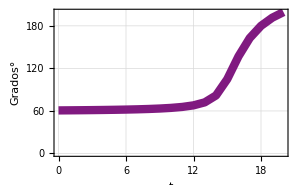

```mathematica
Tabla1=Table[{t, (θ1/.VartArt[t])/Degree},{t,0,tf,1}];
Theta1=Grafica[Tabla1,.5,.1,.5,"t", "Grados°"]
```

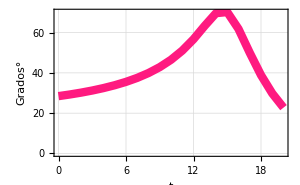

```mathematica
Tabla2=Table[{t, (θ2/.VartArt[t])/Degree},{t,0,tf,1}];
Theta2=Grafica[Tabla2,1,.1,.5,"t", "Grados°"]
```

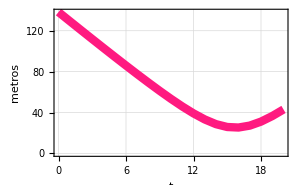

```mathematica
Tabla3=Table[{t, (d3/.VartArt[t])},{t,0,tf,1}];
Theta3=Grafica[Tabla3,1,.1,.5,"t", "metros"]
```

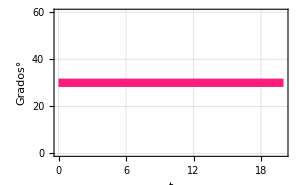

```mathematica
Tabla4=Table[{t, (θ4/.VartArt[t])/Degree},{t,0,tf,1}];
Theta4=Grafica[Tabla4,1,.1,.5,"t", "Grados°"]
```

```mathematica
Tabla5=Table[{t, (θ5/.VartArt[t])/Degree},{t,0,tf,1}];
Theta5=Grafica[Tabla5,1,.1,.5,"t", "Grados°"]
```

-Graphics-

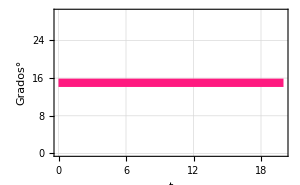

```mathematica
Tabla6=Table[{t, (θ6/.VartArt[t])/Degree},{t,0,tf,1}];
Theta6=Grafica[Tabla6,1,.1,.5,"t", "Grados°"]
```